```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-60==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

## Comparison ν_0.05 for N = 50 and N =60

## μ =20 N =60

```mathematica
μ:=20
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕs[t]/μ)^p)
Vp[t_]=D[V[t],ϕs[t]];
ten := 4.57 10^6
(*ϕsr,asr*)
sol=NDSolve[{ 3 as'[t]/as[t] ϕs[t]+Vp[t]==0,
as'[t]==as[t]Sqrt[1/3 (V[t])], 
ϕs[0]==ϕini,as[0]==1},{ϕs,as},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕs/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {11.838} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

```mathematica
tend
```

4.43542×10^6

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
```

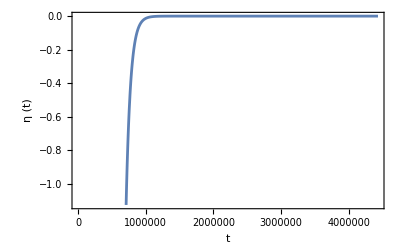

```mathematica
etavst =Plot[{η[t]},{t,0, tend},Frame->True, FrameLabel->{"t", "η (t)"},BaseStyle->{FontFamily->"Times",FontSize->15}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\etavst.pdf", etavst,"PDF"]
```

C:\Users\RAUL\Documents\etavst.pdf

```mathematica
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
hc0 =hc[0.05]//N
```

523500.

```mathematica
xs[t_] = x2[0.05][t]
ys[t_] = y2[0.05][t]
```

6
InterpolatingFunction[{{26175., 1.5705 10 }}, <>][t]

6
InterpolatingFunction[{{26175., 1.5705 10 }}, <>][t]

## μ = 20 N = 50

```mathematica
μ:=20
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕs[t]/μ)^p)
Vp[t_]=D[V[t],ϕs[t]];
ten := 3.79 10^6
(*ϕsr,asr*)
sol=NDSolve[{ 3 as'[t]/as[t] ϕs[t]+Vp[t]==0,
as'[t]==as[t]Sqrt[1/3 (V[t])], 
ϕs[0]==ϕini,as[0]==1},{ϕs,as},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕs/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {12.3478} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

InterpolatingFunction::dmval: Input value {3.90604×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
tend
```

3.784×10^6

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
```

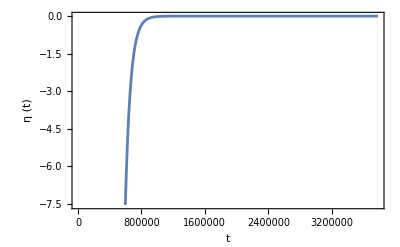

```mathematica
etavst =Plot[{η[t]},{t,0, tend},Frame->True, FrameLabel->{"t", "η (t)"},BaseStyle->{FontFamily->"Times",FontSize->15}]
```

```mathematica
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
hc1 =hc[0.05]//N;
Print[hc1 ]
```

532390.

```mathematica
xs2[t_] = x2[0.05][t]
ys2[t_] = y2[0.05][t]
```

6
InterpolatingFunction[{{26619.5, 1.59717 10 }}, <>][t]

6
InterpolatingFunction[{{26619.5, 1.59717 10 }}, <>][t]

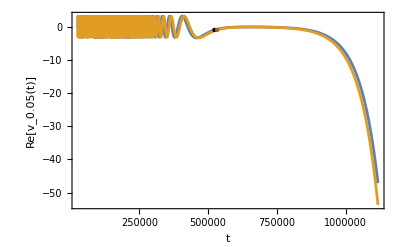

```mathematica
renu00520 =Show[Plot[{xs[t],xs2[t]},{t,tini[0.05], 2.1hc[0.05]} ,Frame->True, FrameLabel->{"t", "Re[v_0.05(t)]"},PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->13}],ListPlot[{ {hc0,xs[hc0]}},PlotStyle->Directive[PointSize[Large],Black]],ListPlot[{ {hc1,xs2[hc1]}},PlotStyle->Directive[PointSize[Large],Brown]]]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\renu00520.pdf", renu00520,"PDF"]
```

C:\Users\RAUL\Documents\renu00520.pdf

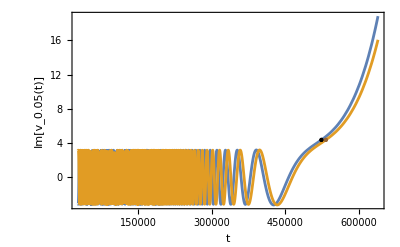

```mathematica
imnu00520 =Show[Plot[{ys[t],ys2[t]},{t,tini[0.05],1.2 hc[0.05]},Frame->True, FrameLabel->{"t", "Im[v_0.05(t)]"},PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->13}],ListPlot[{ {hc0,ys[hc0]}},PlotStyle->Directive[PointSize[Large],Black]],ListPlot[{ {hc1,ys2[hc1]}},PlotStyle->Directive[PointSize[Large],Brown]]]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\imnu00520.pdf", imnu00520,"PDF"]
```

C:\Users\RAUL\Documents\imnu00520.pdf

```mathematica
hc[0.05]//N
ys[523500]
```

532390.

4.36669

```mathematica
hc[0.05]//N
ys[523500]
```

532390.

4.36669

## Comparison ν_0.05 for μ = 20 and μ = 30

## μ =20

```mathematica
μ:=20
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕs[t]/μ)^p)
Vp[t_]=D[V[t],ϕs[t]];
ten := 4.57 10^6
(*ϕsr,asr*)
sol=NDSolve[{ 3 as'[t]/as[t] ϕs[t]+Vp[t]==0,
as'[t]==as[t]Sqrt[1/3 (V[t])], 
ϕs[0]==ϕini,as[0]==1},{ϕs,as},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕs/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {11.838} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

```mathematica
tend
```

4.43542×10^6

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
```

```mathematica
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
hc0 =hc[0.05]//N
tini0 = tini[0.05]//N
```

523500.

26175.

```mathematica
xs[t_] = x2[0.05][t]
ys[t_] = y2[0.05][t]
```

6
InterpolatingFunction[{{26175., 1.5705 10 }}, <>][t]

6
InterpolatingFunction[{{26175., 1.5705 10 }}, <>][t]

## μ = 30

```mathematica
μ:=30
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕs[t]/μ)^p)
Vp[t_]=D[V[t],ϕs[t]];
ten := 3.79 10^6
(*ϕsr,asr*)
sol=NDSolve[{ 3 as'[t]/as[t] ϕs[t]+Vp[t]==0,
as'[t]==as[t]Sqrt[1/3 (V[t])], 
ϕs[0]==ϕini,as[0]==1},{ϕs,as},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕs/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {20.9687} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndsz: At t == -76715.8, step size is effectively zero; singularity or stiff system suspected.

```mathematica
tend
```

3.69781×10^6

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
```

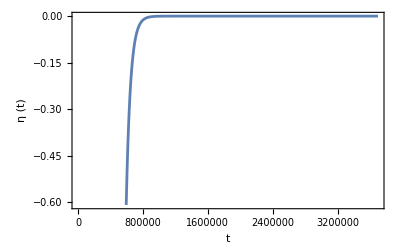

```mathematica
etavst =Plot[{η[t]},{t,0, tend},Frame->True, FrameLabel->{"t", "η (t)"},BaseStyle->{FontFamily->"Times",FontSize->15}]
```

```mathematica
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
hc1 =hc[0.05]//N
tini1 = tini[0.05]//N
```

409943.

20497.1

```mathematica
xs2[t_] = x2[0.05][t]
ys2[t_] = y2[0.05][t]
```

6
InterpolatingFunction[{{20497.1, 1.22983 10 }}, <>][t]

6
InterpolatingFunction[{{20497.1, 1.22983 10 }}, <>][t]

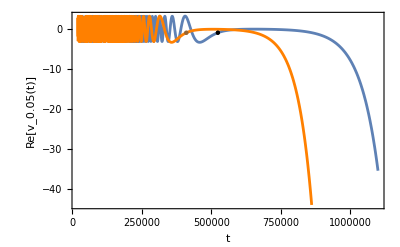

```mathematica
renu0052030 =Show[Plot[{xs[t]},{t,tini0, 2.1hc0} ,Frame->True, FrameLabel->{"t", "Re[v_0.05(t)]"},PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->13}],Plot[{xs2[t]},{t,tini1, 2.1hc1} ,Frame->True, FrameLabel->{"t", "Re[v_0.05(t)]"},PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Orange,_}],ListPlot[{ {hc0,xs[hc0]}},PlotStyle->Directive[PointSize[Large],Black]],ListPlot[{ {hc1,xs2[hc1]}},PlotStyle->Directive[PointSize[Large],Brown]]]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\renu0052030.pdf", renu0052030,"PDF"]
```

C:\Users\RAUL\Documents\renu0052030.pdf

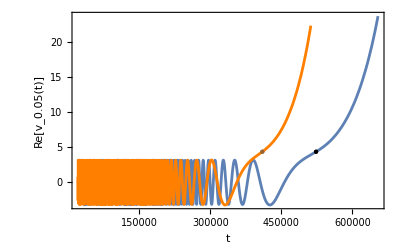

```mathematica
imnu0052030 =Show[Plot[{ys[t]},{t,tini0, 1.25hc0} ,Frame->True, FrameLabel->{"t", "Re[v_0.05(t)]"},PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->13}],Plot[{ys2[t]},{t,tini1, 1.25hc1} ,Frame->True, FrameLabel->{"t", "Im[v_0.05(t)]"},PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Orange,_}],ListPlot[{ {hc0,ys[hc0]}},PlotStyle->Directive[PointSize[Large],Black]],ListPlot[{ {hc1,ys2[hc1]}},PlotStyle->Directive[PointSize[Large],Brown]]]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\imnu0052030.pdf", imnu0052030,"PDF"]
```

C:\Users\RAUL\Documents\imnu0052030.pdf

```mathematica
hc[0.05]//N
ys[523500]
```

523500.

4.36669

```mathematica
hc[0.05]//N
ys[523500]
```

532390.

4.36669

## Plot of M

```mathematica
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"];
```

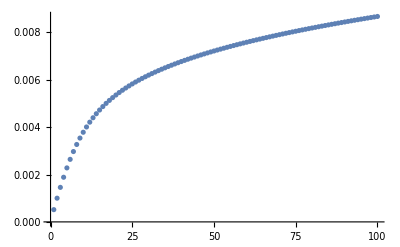

```mathematica
M//ListPlot
```